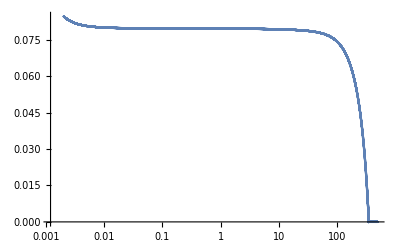

```mathematica
SetDirectory[NotebookDirectory[]];
k=Flatten[Import["./k1.dat"]];
kappa=Flatten[Import["./y13.dat"]]*197.33^2;
ListLinePlot[{Transpose[{k,kappa/(107.580524k)}]},ScalingFunctions->{"Log",Automatic},PlotRange->{All,All}]
```